```mathematica
ou
```

# Cálculo de Capacitâncias em Linhas de Transmissão Aéreas

## Funcões Auxiliares

```mathematica
eliminaPR[m_?MatrixQ,nc_,np_]:=Take[Inverse[m],nc-np,nc-np]

eliminaFeixe[aux_?MatrixQ,nb_,nf_]:=Table[Sum[aux[[i,j]],{i,nb*m-(nb-1),nb*m},{j,nb*n-(nb-1),nb*n}],{m,nf},{n,1,nf}]
(*Matriz de Coeficientes de Potencial*)MPot[(x_)?VectorQ,(y_)?VectorQ,nc_,npr_,rf_,rpr_]:=Table[If[i≠j,(1/2)*Log[((x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],If[i≤nc-npr,Log[(2*y[[i]])/rf],Log[(2*y[[i]])/rpr]]],{i,1,nc},{j,1,nc}]

(*Matriz de Coeficientes de Potencial para lt sem pr*)
MPot2[(x_)?VectorQ,(y_)?VectorQ,nc_,rf_]:=Table[If[i≠j,(1/2)*Log[((x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],Log[(2*y[[i]])/rpr]],{i,1,nc},{j,1,nc}]

ϕ1={{0,1,0},{0,0,1},{1,0,0}};

Qϕ=ArrayFlatten[{{ϕ1,0},{0,ϕ1}}];
A=With[{a=Exp[I 120 Degree]},{{1,1,1},{1,a^2,a},{1,a,a^2}}];
```

## Constantes

```mathematica
μ=4 π 10^-7;
ϵ=8.854 10^-12;
```

## Configuracão da LT

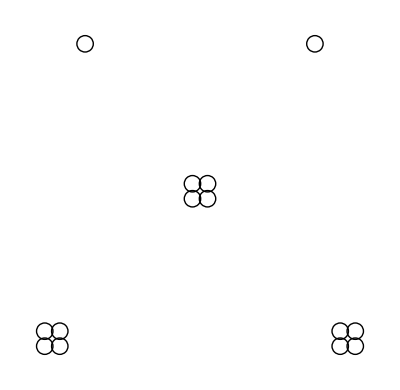

```mathematica
xy={{-4.271,10.771},{-4.271,11.229},{-4.729,11.229},{-4.729,10.771},{0.229,15.271},{0.229,15.729},{-0.229,15.729},{-0.229,15.271},{4.271,10.771},{4.271,11.229},{4.729,11.229},{4.729,10.771},{-3.500,20.000},{3.500,20.000}};

mostra1={Circle[#,.25]}&/@xy;

t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
xc=xy[[All,1]];

yc=xy[[All,2]];

ncond=Length[xc];
npr=2;
nfeixe=4;
nfases=3;

rf=29.591*10^-3/2;
r0=(7.3914/2*10^-3);
ρc=6.114292531162*10^-5 Pi*(rf^2-r0^2);
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
ρpr=Rdcpr*Pi*rpr^2;
ρsolo=1000.;
σsolo=1/ρsolo;
```

## Cálculos das Matrizes

```mathematica
ω=2 π 60.;
```

calculo da matrix de coeficientes de potencial

```mathematica
P=MPot[xc,yc,ncond,2,rf,rpr];
MatrixForm[P]
```

(7.28344 | 3.87193 | 3.52557 | 3.85112 | 1.42377 | 1.3899 | 1.43284 | 1.47176 | 0.998026 | 1.01482 | 0.969895 | 0.953221 | 1.20106 | 0.967182
3.87193 | 7.32508 | 3.89274 | 3.52557 | 1.4915 | 1.45737 | 1.50554 | 1.54533 | 1.01482 | 1.03421 | 0.98889 | 0.969895 | 1.26635 | 1.01023
3.52557 | 3.89274 | 7.32508 | 3.87193 | 1.43854 | 1.40945 | 1.45737 | 1.4915 | 0.969895 | 0.98889 | 0.946423 | 0.927807 | 1.26095 | 0.987765
3.85112 | 3.52557 | 3.87193 | 7.28344 | 1.37605 | 1.34677 | 1.3899 | 1.42377 | 0.953221 | 0.969895 | 0.927807 | 0.91128 | 1.19623 | 0.946248
1.42377 | 1.4915 | 1.43854 | 1.37605 | 7.63253 | 4.21487 | 3.86841 | 4.2001 | 1.47176 | 1.54533 | 1.4915 | 1.42377 | 1.77314 | 1.81814
1.3899 | 1.45737 | 1.40945 | 1.34677 | 4.21487 | 7.66209 | 4.22965 | 3.86841 | 1.43284 | 1.50554 | 1.45737 | 1.3899 | 1.84622 | 1.89751
1.43284 | 1.50554 | 1.45737 | 1.3899 | 3.86841 | 4.22965 | 7.66209 | 4.21487 | 1.3899 | 1.45737 | 1.40945 | 1.34677 | 1.89751 | 1.84622
1.47176 | 1.54533 | 1.4915 | 1.42377 | 4.2001 | 3.86841 | 4.21487 | 7.63253 | 1.42377 | 1.4915 | 1.43854 | 1.37605 | 1.81814 | 1.77314
0.998026 | 1.01482 | 0.969895 | 0.953221 | 1.47176 | 1.43284 | 1.3899 | 1.42377 | 7.28344 | 3.87193 | 3.52557 | 3.85112 | 0.967182 | 1.20106
1.01482 | 1.03421 | 0.98889 | 0.969895 | 1.54533 | 1.50554 | 1.45737 | 1.4915 | 3.87193 | 7.32508 | 3.89274 | 3.52557 | 1.01023 | 1.26635
0.969895 | 0.98889 | 0.946423 | 0.927807 | 1.4915 | 1.45737 | 1.40945 | 1.43854 | 3.52557 | 3.89274 | 7.32508 | 3.87193 | 0.987765 | 1.26095
0.953221 | 0.969895 | 0.927807 | 0.91128 | 1.42377 | 1.3899 | 1.34677 | 1.37605 | 3.85112 | 3.52557 | 3.87193 | 7.28344 | 0.946248 | 1.19623
1.20106 | 1.26635 | 1.26095 | 1.19623 | 1.77314 | 1.84622 | 1.89751 | 1.81814 | 0.967182 | 1.01023 | 0.987765 | 0.946248 | 9.07712 | 1.75805
0.967182 | 1.01023 | 0.987765 | 0.946248 | 1.81814 | 1.89751 | 1.84622 | 1.77314 | 1.20106 | 1.26635 | 1.26095 | 1.19623 | 1.75805 | 9.07712)

eliminação dos cabos para-raios: método "direto"

```mathematica
CsemPR=eliminaPR[P,ncond,2];
```

eliminação dos cabos para-raios: reducao de Kron

```mathematica
Pred=P[[1;;12,1;;12]]-P[[1;;12,13;;14]].Inverse[P[[13;;14,13;;14]]].P[[13;;14,1;;12]];
Cred=Inverse[Pred];
MatrixForm[Cred-CsemPR]
```

(-2.77556×10^-17 | -5.55112×10^-17 | 6.93889×10^-18 | 1.38778×10^-17 | -4.33681×10^-19 | 4.33681×10^-18 | 5.63785×10^-18 | -2.60209×10^-18 | 6.93889×10^-18 | 3.46945×10^-18 | -3.25261×10^-18 | -6.28837×10^-18
-2.77556×10^-17 | 2.77556×10^-17 | -2.77556×10^-17 | 2.77556×10^-17 | 2.60209×10^-18 | -1.30104×10^-18 | -1.21431×10^-17 | 6.07153×10^-18 | -2.1684×10^-18 | 2.60209×10^-18 | -1.73472×10^-18 | 4.55365×10^-18
0. | -5.55112×10^-17 | 2.77556×10^-17 | 4.16334×10^-17 | -2.1684×10^-18 | -2.1684×10^-18 | 8.67362×10^-19 | 0. | 6.28837×10^-18 | 4.33681×10^-19 | -1.51788×10^-18 | -2.60209×10^-18
-4.16334×10^-17 | 1.38778×10^-17 | 0. | 2.77556×10^-17 | 3.46945×10^-18 | -8.67362×10^-19 | 1.30104×10^-18 | -1.30104×10^-18 | -1.30104×10^-18 | 1.73472×10^-18 | 2.1684×10^-18 | -3.25261×10^-18
-5.20417×10^-18 | 6.07153×10^-18 | -9.1073×10^-18 | 6.93889×10^-18 | 5.55112×10^-17 | -2.77556×10^-17 | 1.38778×10^-17 | -1.38778×10^-17 | 6.07153×10^-18 | -7.80626×10^-18 | 1.21431×10^-17 | -1.73472×10^-17
1.47451×10^-17 | -9.1073×10^-18 | 9.97466×10^-18 | -7.37257×10^-18 | -5.55112×10^-17 | 5.55112×10^-17 | -1.38778×10^-17 | -1.38778×10^-17 | -7.80626×10^-18 | 1.47451×10^-17 | -9.1073×10^-18 | 9.54098×10^-18
2.1684×10^-18 | -8.67362×10^-19 | -3.90313×10^-18 | 1.0842×10^-17 | 1.38778×10^-17 | -6.93889×10^-17 | 5.55112×10^-17 | 0. | 6.93889×10^-18 | 4.33681×10^-19 | -4.33681×10^-18 | -4.77049×10^-18
1.73472×10^-18 | -5.20417×10^-18 | 6.07153×10^-18 | -9.97466×10^-18 | 0. | -6.93889×10^-18 | 0. | 0. | 2.1684×10^-18 | -4.77049×10^-18 | 4.33681×10^-19 | 1.12757×10^-17
-4.33681×10^-19 | 3.03577×10^-18 | 8.67362×10^-19 | -7.80626×10^-18 | 6.07153×10^-18 | -1.17094×10^-17 | 1.73472×10^-18 | 1.30104×10^-17 | -8.32667×10^-17 | 9.71445×10^-17 | 6.93889×10^-18 | -1.38778×10^-17
6.50521×10^-18 | 1.73472×10^-18 | -1.0842×10^-18 | -2.60209×10^-18 | 1.04083×10^-17 | -6.07153×10^-18 | -1.0842×10^-17 | 5.20417×10^-18 | 5.55112×10^-17 | -1.11022×10^-16 | 6.93889×10^-17 | -1.38778×10^-17
-3.90313×10^-18 | -5.20417×10^-18 | 5.63785×10^-18 | 4.98733×10^-18 | 8.67362×10^-18 | -6.93889×10^-18 | -6.07153×10^-18 | -5.20417×10^-18 | 0. | 6.93889×10^-17 | -8.32667×10^-17 | 1.38778×10^-17
-1.30104×10^-18 | 5.63785×10^-18 | -4.33681×10^-18 | 4.33681×10^-18 | -2.90566×10^-17 | 2.86229×10^-17 | 6.93889×10^-18 | -3.46945×10^-18 | 0. | -3.46945×10^-17 | 0. | 2.77556×10^-17)

eliminação dos feixes

```mathematica
Yabc=ⅉ ω 2.0 π ϵ eliminaFeixe[CsemPR,nfeixe,nfases];
```

```mathematica
MatrixForm[Yabc]
```

(5.12287×10^-9 ⅈ | -1.10394×10^-9 ⅈ | -6.04459×10^-10 ⅈ
-1.10394×10^-9 ⅈ | 5.34596×10^-9 ⅈ | -1.10394×10^-9 ⅈ
-6.04459×10^-10 ⅈ | -1.10394×10^-9 ⅈ | 5.12287×10^-9 ⅈ)

```mathematica
Y012=DiagonalMatrix[Diagonal[Inverse[A].Yabc.A]];
```

```mathematica
MatrixForm[Y012]
```

(9.84235×10^-27+3.32234×10^-9 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 4.3944×10^-25+6.13468×10^-9 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -2.32645×10^-25+6.13468×10^-9 ⅈ)

```mathematica
MatrixForm[Y012 10^6//Im]
```

(0.00332234 | 0. | 0.
0. | 0.00613468 | 0.
0. | 0. | 0.00613468)

## Cálculos das Matrizes Utilizando RMG

raio do feixe

```mathematica
Rf=(.458/2) /Cos[45 Degree];
Rmg=(nfeixe*rf*Rf^(nfeixe-1))^(1/nfeixe)
```

0.211744

Novas coordenadas dos condutores

```mathematica
xc1={-4.042,0,4.042,-3.500,3.5};
yc1={10.52, 15.5, 10.52, 20,20};
P1=MPot[xc1,yc1,5,2,Rmg,rpr];
MatrixForm[P1]
```

(4.5988 | 1.41232 | 1.02539 | 1.16772 | 0.953647
1.41232 | 4.98637 | 1.41232 | 1.83375 | 1.83375
1.02539 | 1.41232 | 4.5988 | 0.953647 | 1.16772
1.16772 | 1.83375 | 0.953647 | 9.07712 | 1.75805
0.953647 | 1.83375 | 1.16772 | 1.75805 | 9.07712)

```mathematica
CsemPR1=eliminaPR[P1,5,2];
Yabc1=ⅉ ω 2.0 π ϵ CsemPR1;
MatrixForm[Yabc1]
```

(5.1705×10^-9 ⅈ | -1.07646×10^-9 ⅈ | -7.08836×10^-10 ⅈ
-1.07646×10^-9 ⅈ | 5.32338×10^-9 ⅈ | -1.07646×10^-9 ⅈ
-7.08836×10^-10 ⅈ | -1.07646×10^-9 ⅈ | 5.1705×10^-9 ⅈ)

```mathematica
Y012x=DiagonalMatrix[Diagonal[Inverse[A].Yabc1.A]];
 MatrixForm[Y012x 10^6//Im]
```

(0.00331363 | 0. | 0.
0. | 0.00617538 | 0.
0. | 0. | 0.00617538)

```mathematica
MatrixForm[(Y012x -Y012) 10^6//Im]
```

(-8.70771×10^-6 | 0. | 0.
0. | 0.0000406952 | 0.
0. | 0. | 0.0000406952)